-Graphics-

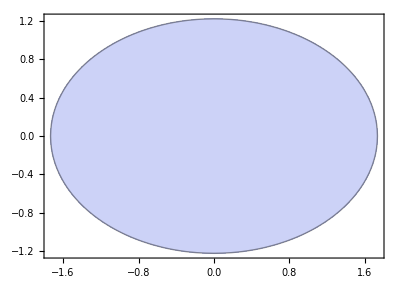

```mathematica
(*Построим область интегрирования*)
RegionPlot[x^2+2*y^2≤3,{x,-Sqrt[3],Sqrt[3]},{y,-Sqrt[3/2],Sqrt[3/2]},AspectRatio->Automatic]
```

```mathematica
(*Зададим подынтегральную функцию и построим ее график над областью интегрирования*)
f[x_,y_]=x^2+y^2;
Plot3D[f[x,y],{x,-Sqrt[3],Sqrt[3]},{y,-Sqrt[3/2],Sqrt[3/2]},RegionFunction->Function[{x,y,z},x^2+2*y^2≤3]]
```

-Graphics3D-

```mathematica
(*Зададим преобразование прямоугольника [-Sqrt[3];Sqrt[3]]x[-Sqrt[3/2];Sqrt[3/2]], содержащего область интегрирования, в квадрат [0;1]x[0;1]*)
u[x_,y_]=Sqrt[3]/6*x+1/2;
v[x_,y_]=Sqrt[6]/6*y+1/2;
(*Найдем модуль якобиана построенного преобразования*)J[x_,y_]=Abs[Det[{{D[u[x,y],x],D[u[x,y],y]},{D[v[x,y],x],D[v[x,y],y]}}]];
(*Зададим обратное преобразование квадрата [0;1]x[0;1] в прямоугольник [-Sqrt[3];Sqrt[3]]x[-Sqrt[3/2];Sqrt[3/2]]*)
Inv=Solve[{s==u[x,y],t==v[x,y]},{x,y}];
g1[s_,t_]=x/.Inv[[1,1]];
g2[s_,t_]=y/.Inv[[1,2]];
(*Зададим функцию в квадрате [0;1]x[0;1], значения которой в образе области интегрирования совпадают со значениями подынтегральной функции, а в остальных точках квадрата равны нулю*)
F[s_,t_]=If[(g1[s,t])^2+2*(g2[s,t])^2≤3,f[g1[s,t],g2[s,t]],0];
Plot3D[F[s,t],{s,0,1},{t,0,1}]
```

-Graphics3D-

```mathematica
(*Зададим количество точек равномерного распределения*)
n=1000000;
(*Построим равномерное распределение в квадрате [0;1]x[0;1]*)
P=RandomReal[1,{n,2}];
(*Вычислим значение двойного интеграла, используя метод Монте-Карло*)
Int=1/n*Sum[F[P[[i,1]],P[[i,2]]]*J[g1[P[[i,1]],P[[i,2]]],g2[P[[i,1]],P[[i,2]]]],{i,1,n}];
Print["Значение интеграла равно: ",Int]
```

Значение интеграла равно: 0.104131